```mathematica
(* Created with Mathematica 8.0.1 *)
(* Code version 1.3 // Subscript[f, Starob](R)CDM *)
```

```mathematica
Quit[]
```

```mathematica
(* Definitions *)
```

```mathematica
(* Set the directory *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
Needs["NumericalCalculus`"];
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb];
deaddrop="C:\\Users\\savvas\\Dropbox\\Work\\leavas";
```

```mathematica
(* Various scales and data *)
```

```mathematica
(* Maximum Likelihood value for Ωb*h^2 from WMAP7 *)
Ωbh2=2.258/100;
h=0.704;
ob0=Ωbh2/h^2;
```

```mathematica
(* Subscript[Ω, r]=Subscript[Ω, γ]+Subscript[Ω, ν] see PDG *) 
Ωγ=2.469 10^-5 h^-2;Neff=3.04;Ωr=Ωγ(1+0.2271 Neff);
(* E=H/H0 for the Starobinsky model (n=1) under the BNP approximation *) 
H[a_?NumberQ,om_?NumberQ,flat_?NumberQ,b_?NumberQ,nothing1_?NumberQ]:=Sqrt[1-om+om/a^3-Ωr+Ωr/a^4+(a^5 b^2 (-1+om+Ωr)^3 (-37 a om^2-40 om Ωr+32 a^4 om (-1+om+Ωr)+16 a^3 Ωr (-1+om+Ωr)+32 a^7 (-1+om+Ωr)^2))/(om-4 a^3 (-1+om+Ωr))^4+(a^11 b^4 (-1+om+Ωr)^5 (123 a om^6+128 om^5 Ωr-82748 a^4 om^5 (-1+om+Ωr)-160440 a^3 om^4 Ωr (-1+om+Ωr)-77760 a^2 om^3 Ωr^2 (-1+om+Ωr)-44552 a^7 om^4 (-1+om+Ωr)^2-277568 a^6 om^3 Ωr (-1+om+Ωr)^2-228096 a^5 om^2 Ωr^2 (-1+om+Ωr)^2+289024 a^10 om^3 (-1+om+Ωr)^3+310144 a^9 om^2 Ωr (-1+om+Ωr)^3-82944 a^8 om Ωr^2 (-1+om+Ωr)^3-234880 a^13 om^2 (-1+om+Ωr)^4-6144 a^12 om Ωr (-1+om+Ωr)^4+63488 a^16 om (-1+om+Ωr)^5+20480 a^15 Ωr (-1+om+Ωr)^5+20480 a^19 (-1+om+Ωr)^6))/(om-4 a^3 (-1+om+Ωr))^10]
(* f(R) model and Geff *)
Ra[a_,om_,b_]:=6(2 H[a,om,0,b,0]^2+H[a,om,0,b,0] a D[H[aa,om,0,b,0],aa])/.aa->a//Re
f[R_]:=R-2Λ (1- 1/((1+(R/(b Λ))^2)^n))/.Λ->3(1-om-or)/.n->1
Geff=1/f'[R](1+4 k^2/a^2 f''[R]/f'[R])/(1+3 k^2/a^2 f''[R]/f'[R])/.k->0.1;
Geffz[z_,om1_,b1_]:=Geff/.b->b1/.om->om1/.or->Ωr/.R->Ra[1/(1+z),om1,b1]/.a->1/(1+z)
(* Sound speed *) cs[a_?NumberQ,ob_?NumberQ]:=1/√(3(1+((3ob)/(4Ωγ))a));
```

```mathematica
fk[x_?NumberQ,ok_?NumberQ]:=Sin[√Abs[ok] x]/(√Abs[ok])/;ok<0
fk[x_?NumberQ,ok_?NumberQ]:=x/;ok==0
fk[x_?NumberQ,ok_?NumberQ]:=Sinh[√Abs[ok] x]/(√Abs[ok])/;ok>0
(* Alternatively 1/(√-ok)Sin[√-ok x] would work just as well *)
```

```mathematica
(* Redshift at decoupling (see Eqs. (66)-(68) in Komatsu et al.2009) *)
zcmb[om_?NumberQ,ob_?NumberQ]:=1048(1+0.00124(ob h^2)^-0.738)(1+((0.0783(ob h^2)^-0.238)/(1+39.5(ob h^2)^0.763))(om h^2)^(0.560/(1+21.1(ob h^2)^1.81)))
(* Drag redshift (see Eq. (4) of Hu astro-ph/9709112) *)
zdrag[om_?NumberQ,ob_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(ob h^2)^(0.238(om h^2)^0.223))
(* Proper (not comoving) angular diameter distance with curvature, see Komatsu et al. 0803.0547  *)
DA[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=1/(1+z)fk[NIntegrate[1/H[1/(1+z1),om,ok,w0,wa],{z1,0,z}],ok]
(* Comoving sound horizon at drag redshift (see Percival et al: 0907.1660 Section 6 *)
rs[ze_,om_?NumberQ,ok_?NumberQ,ob_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=NIntegrate[cs[x,ob]/(x^2H[x,om,ok,w0,wa]),{x,0,1/(1+ze[om,ob])}]
(* Dilation scale *)
Dv[zbao_,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=((DA[zbao,om,ok,w0,wa](1+zbao))^2 zbao/H[1/(1+zbao),om,ok,w0,wa])^(1/3)
(* Scaled distance at recombination *)
R[om_,ok_,ob_,w0_,wa_]:=√om DA[zcmb[om,ob],om,ok,w0,wa](1+zcmb[om,ob])
(* Angular scale of sound horizon at recombination *)
la[om_,ok_,ob_,w0_,wa_]:=π (DA[zcmb[om,ob],om,ok,w0,wa](1+zcmb[om,ob]))/rs[zcmb,om,ok,ob,w0,wa]
(* Distance for SnIa calculation *)
 rr[xx_,om_,ok_,w0_,wa_]:=DA[xx,om,ok,w0,wa](1+xx)
```

```mathematica
(* CMB and BAO χ^2 terms *)
```

```mathematica
(* CMB: WMAP9 *)
```

```mathematica
(* Central values and 1-σ errors for {Subscript[l, a], R, zcmb} from WMAP7 *)
(* See 1212.5226, page 21 for details *)
datacmb={302.40,1.7246,1090.88};
(* Inverse Covariance Matrix using  for {Subscript[l, a], R, zcmb} *)
invcov=({{3.182, 18.253, -1.429}, {18.253, 11887.879, -193.808}, {-1.429, -193.808, 4.556}});
(* χ^2 for R *)
vec[om_,ok_,ob_,b_,wa_]:={la[om,ok,ob,b,wa]-datacmb[[1]],R[om,ok,ob,b,wa]-datacmb[[2]],zcmb[om,ob]-datacmb[[3]]};
chi2R[om_,ok_,b_,wa_]:=vec[om,ok,ob0,b,wa].invcov.vec[om,ok,ob0,b,wa]
```

```mathematica
(* BAO: SDSS 7 + WiggleZ + 6dFGS *)
```

```mathematica
(* BAO data, see 1205.0364 *)
databao={{0.106,0.336,0.015},{0.2,0.1905,0.0061},{0.35,0.1097,0.0036},{0.44,0.0916,0.0071},{0.6,0.0726,0.0034},{0.73,0.0592,0.0032}};
Cijinv=({{4444, 0, 0, 0, 0, 0}, {0, 30318, -17312, 0, 0, 0}, {0, -17312, 87046, 0, 0, 0}, {0, 0, 0, 23857, -22747, 10586}, {0, 0, 0, -22747, 128729, -59907}, {0, 0, 0, 10586, -59907, 125536}});
lBAO[om_,ob_,h_]:=1/(2997.9/h)44.5Log[9.83/(om h^2)]/(√(1+10(ob h^2)^(3/4)));
dz[zbao_,om_,ok_,b_,wa_]:=lBAO[om,ob0,h]/Dv[zbao,om,ok,b,wa]
vecbao[om_,ok_,ob_,b_,wa_]:=Table[(databao[[i,2]]-dz[databao[[i,1]],om,ok,b,wa]),{i,1,Length[databao]}];
chi2bao[om_,ok_,b_,wa_]:=vecbao[om,ok,ob0,b,wa].Cijinv.vecbao[om,ok,ob0,b,wa]
```

```mathematica
(* SnIa χ^2 term *)
```

```mathematica
(* Read the SnIa data *)
```

```mathematica
Off[NIntegrate::"inumr"];Off[NIntegrate::"nlim"];
datasets={Constitution,Union2,Union21};
descript={{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number},{Word,Number,Number,Number,Number,Number,Number,Number,Number,Number},{Word,Number,Number,Number,Number}};
sigmaint={0,0,0};
location={{2,10,11},{2,3,4},{2,3,4}};
Do[datanw[ds]=ReadList[".\\data\\"<>ToString[datasets[[ds]]]<>".txt",descript[[ds]]];,{ds,1,Length[datasets]}];
set=3;
ndat=Length[datanw[set]];
data=datanw[set][[All,location[[set]]]];
sint=sigmaint[[set]];
```

```mathematica
(* chi^2 // minimize over h *)
```

```mathematica
chi2fa[om_,ok_,b_,wa_]:=Sum[(data[[i,2]]-5 Log[10,rr[data[[i,1]],om,ok,b,wa]*(1+data[[i,1]])])^2/(data[[i,3]]^2+sint^2),{i,1,ndat}];
chi2fb[om_,ok_,b_,wa_]:=Sum[(data[[i,2]]-5 Log[10,rr[data[[i,1]],om,ok,b,wa]*(1+data[[i,1]])])/(data[[i,3]]^2+sint^2),{i,1,ndat}];
chi2fc=Sum[1/(data[[i,3]]^2+sint^2),{i,1,ndat}];
chi2SN[om_,ok_,b_,wa_]:=chi2fa[om,ok,b,wa]-chi2fb[om,ok,b,wa]^2/chi2fc;
```

```mathematica
(* Growth rate χ^2 term *)
```

```mathematica
(* The growth rate data *)
```

```mathematica
datagrowth={{0.02,0.36,0.04},{0.067,0.423,0.055},{0.17,0.51,0.06},{0.35,0.44,0.05},{0.77,0.49,0.18},{0.25,0.3512,0.0583},{0.37,0.4602,0.0378},{0.22,0.42,0.07},{0.41,0.45,0.04},{0.6,0.43,0.04},{0.78,0.38,0.04},{0.57,0.451,0.025},{0.3,0.407,0.055},{0.4,0.419,0.041},{0.5,0.427,0.043},{0.6,0.433,0.067}};
```

```mathematica
(* chi^2 part *)
```

```mathematica
(* Various models for γ(z) *)
γ[0][z_,g0_,g1_]:=g0
γ[1][z_,g0_,g1_]:=(g0+g1 z)/;z≤0.5
γ[1][z_,g0_,g1_]:=(g0+g1/2)/;z>0.5
γ[2][z_,g0_,g1_]:=(g0+g1 z/(1+z))
```

```mathematica
(* The growth rate and fσ8 (A in the paper) *)
fgrowth[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,gammamodel_]:=((om (1+z)^3)/H[1/(1+z),om,ok,w0,wa]^2)^γ[gammamodel][z,γ0,γ1]
fσ8z[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=σ8 Exp[NIntegrate[1/aa fgrowth[1/aa-1,om,ok,w0,wa,γ0,γ1,gammamodel],{aa,1,1/(1+z)}]] fgrowth[z,om,ok,w0,wa,γ0,γ1,gammamodel]
```

```mathematica
(* Same as above but for wCDM models *)
δ[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[z_,w_,Ω_]:=aa D[Log[δ[aa,w,Ω]],aa]/.aa->1/(1+z)
fσ8wCDM[z_,w_,Ω_,σ8_]:=fwCDM[z,w,Ω]σ8  δ[1/(1+z),w,Ω]/δ[1,w,Ω]
```

```mathematica
(* The chi^2 *)
chi2growth[om_?NumberQ,ok_?NumberQ,b_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=Sum[(1/datagrowth[[i,3]](datagrowth[[i,2]]-fσ8z[datagrowth[[i,1]],om,ok,b,wa,γ0,γ1,σ8,gammamodel]))^2,{i,1,Length[datagrowth]}]
```

```mathematica
(* end *)
```

```mathematica
(* Combine all data (SnIa, CMB, BAO, Growth) *)
```

```mathematica
chi2total[om_?NumberQ,ok_?NumberQ,b_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=chi2R[om,ok,b,wa]+chi2bao[om,ok,b,wa]+ chi2SN[om,ok,b,wa]+chi2growth[om,ok,b,wa,γ0,γ1,σ8,gammamodel]
```

```mathematica
(* Cache *)
```

```mathematica
σ80=0.8;
fmin1={3263.3541318`10.965209198494833,{574.1778674338526,{om->0.27153193979219903,b->0.2916569762078968,g0->0.5941305691257319}}};
fmin2={3332.6806566`10.974338694278924,{573.8574029997583,{om->0.2721520548455338,b->0.1500426850303717,g0->0.5665291229120537,g1->0.11337718357358352}}};
fmin3={2076.7848476`10.768936499978095,{573.7654208677827,{om->0.27215754298902184,b->0.14915964098120568,g0->0.5614584042639404,g1->0.17880580095425555}}};
```

```mathematica
cij1={{0.000022057534262098553,-0.0023106643977098772,0.00006535659334008792},{-0.0023106643977098772,0.41826246182946564,-0.008479869672395654},{0.00006535659334008797,-0.008479869672395661,0.002248113430963139}};
cij2={{0.000023535272123468684,-0.005104801875276451,0.000011063031543310999,0.00022916336836444496},{-0.005104801875276451,1.8367288483297861,0.0014019745069949185,-0.07700295576272309},{0.00001106303154331107,0.0014019745069949131,0.004411462774398814,-0.009365537482745412},{0.0002291633683644449,-0.07700295576272312,-0.009365537482745412,0.039769379512354326}};
cij3={{0.000021481005633367955,-0.004391151440375178,9.222266916890528*^-6,0.0002802871080498188},{-0.004391151440375177,1.589265547387716,0.001972352176725839,-0.09349413892590408},{9.222266916890555*^-6,0.0019723521767257488,0.004615498225212967,-0.013752621684652163},{0.00028028710804981854,-0.09349413892590397,-0.01375262168465217,0.0775774928701173}};
```

```mathematica
(* end *)
```

```mathematica
(* Tests *)
```

```mathematica
?chi2total
```

Global`chi2total

chi2total[om_?NumberQ,ok_?NumberQ,b_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=chi2R[om,ok,b,wa]+chi2bao[om,ok,b,wa]+chi2SN[om,ok,b,wa]+chi2growth[om,ok,b,wa,γ0,γ1,σ8,gammamodel]

```mathematica
(* Prefered range for b~0.1 *)
```

```mathematica
chi2SN[0.24,0,0.1,0]//AbsoluteTiming
chi2SN[0.25,0,0.1,0]//AbsoluteTiming
```

{6.0073436,566.077}

{5.9183385,564.241}

```mathematica
chi2R[0.24,0,0.1,0]//AbsoluteTiming
chi2R[0.25,0,0.1,0]//AbsoluteTiming
```

{0.151009,127.156}

{0.151009,56.4983}

```mathematica
chi2bao[.24,0,0.1,0]//AbsoluteTiming
chi2bao[.25,0,0.1,0]//AbsoluteTiming
```

{0.0630036,5.94675}

{0.0640037,4.89557}

```mathematica
chi2growth[0.24,0,0.1,0,6/11,0,0.8,0]//AbsoluteTiming
chi2growth[0.25,0,0.1,0,6/11,0.1,0.8,1]//AbsoluteTiming
chi2growth[0.25,0,0.1,0,6/11,0.1,0.8,2]//AbsoluteTiming
```

{0.0980056,8.28207}

{0.141008,8.29724}

{0.104006,8.10836}

```mathematica
chi2total[0.27,0,0.1,0,6/11,0,σ80,0]//AbsoluteTiming
chi2total[0.27,0,0.1,0,6/11,0.1,σ80,1]//AbsoluteTiming
chi2total[0.27,0,0.1,0,6/11,0.1,σ80,2]//AbsoluteTiming
```

{6.2813593,575.862}

{7.569433,574.631}

{6.8103896,574.775}

```mathematica
(* end *)
```

```mathematica
(* Minimization *)
```

```mathematica
?chi2total
```

Global`chi2total

chi2total[om_?NumberQ,ok_?NumberQ,b_?NumberQ,wa_?NumberQ,γ0_?NumberQ,γ1_?NumberQ,σ8_?NumberQ,gammamodel_]:=chi2R[om,ok,b,wa]+chi2bao[om,ok,b,wa]+chi2SN[om,ok,b,wa]+chi2growth[om,ok,b,wa,γ0,γ1,σ8,gammamodel]

```mathematica
σ80=0.8;
```

```mathematica
(* Γ0 // Om, γ0, γ1=0, σ8 *)
fmin1=FindMinimum[chi2total[Abs[om],0,b,0,g0,0,σ80,0],{om,0.27,0.271},{b,0.11,0.111},{g0,0.583,0.584}]//AbsoluteTiming
```

{3263.354132,{574.178,{om→0.271532,b→0.291657,g0→0.594131}}}

```mathematica
(* Γ1 // Om, γ0, γ1, σ8 *)
fmin2=FindMinimum[chi2total[Abs[om],0,b,0,g0,g1,σ80,1],{om,0.268,0.269},{b,0.09,0.095},{g0,.575,0.576},{g1,.1,0.11}]//AbsoluteTiming
```

{3332.680657,{573.857,{om→0.272152,b→0.150043,g0→0.566529,g1→0.113377}}}

```mathematica
(* Γ2 // Om, γ0, γ1, σ8 *)
fmin3=FindMinimum[chi2total[Abs[om],0,b,0,g0,g1,σ80,2],{om,0.268,0.269},{b,0.09,0.095},{g0,.575,0.576},{g1,.1,0.11}]//AbsoluteTiming
```

{2076.784848,{573.765,{om→0.272158,b→0.14916,g0→0.561458,g1→0.178806}}}

```mathematica
(* end *)
```

```mathematica
(* Errors+errorbars *)
```

```mathematica
(* Γ0 *)
```

```mathematica
Clear[om0,g00,g10,params]
om0=fmin1[[2,2,1,2]];
b0=fmin1[[2,2,2,2]];
g00=fmin1[[2,2,3,2]];
params={om,b,g0};
```

```mathematica
case0=FunctionInterpolation[chi2total[om,0,b,0,g0,0,σ80,0],{om,om0-0.01,om0+0.01},{b,b0-0.02,b0+0.02},{g0,g00-0.02,g00+0.02}]//AbsoluteTiming;
```

```mathematica
case0[[1]]
```

11892.322568

```mathematica
Export[".\\backups\\chi2_int_Starob_G0.m",case0]
```

.\backups\chi2_int_Starob_G0.m

```mathematica
Fij0=1/2Table[D[case0[[2]][om,b,g0],params[[i]],params[[j]]]/.fmin1[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij0=Inverse[Fij0]
errors0=√Diagonal[cij0]
```

{{109560.,585.456,-976.775},{585.456,5.71731,4.54543},{-976.775,4.54543,490.359}}

{{0.0000220575,-0.00231066,0.0000653566},{-0.00231066,0.418262,-0.00847987},{0.0000653566,-0.00847987,0.00224811}}

{0.00469654,0.646732,0.0474143}

```mathematica
(* end *)
```

```mathematica
(* Γ1 *)
```

```mathematica
Clear[om0,g00,g10,params]
om0=fmin2[[2,2,1,2]];
b0=fmin2[[2,2,2,2]];
g00=fmin2[[2,2,3,2]];
g10=fmin2[[2,2,4,2]];
params={om,b,g0,g1};
```

```mathematica
LaunchKernels[3];
```

```mathematica
case1=ListInterpolation[ParallelTable[chi2total[om,0,b,0,g0,g1,σ80,1],{om,om0-0.01,om0+0.01,0.01},
{b,b0-0.02,b0+0.02,0.02},{g0,g00-0.02,g00+0.02,0.02},{g1,g10-0.1,g10+0.1,0.1},DistributedContexts->Automatic],{{om0-0.01,om0+0.01},
{b0-0.02,b0+0.02},{g00-0.02,g00+0.02},{g10-0.1,g10+0.1}}]//AbsoluteTiming;
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2, 2, 2, 2}.

```mathematica
case1[[1]]
```

240.786423

```mathematica
Export[".\\backups\\chi2_int_Starob_G1.m",case1]
```

.\backups\chi2_int_Starob_G1.m

```mathematica
Fij1=1/2Table[D[case1[[2]][om,b,g0,g1],params[[i]],params[[j]]]/.fmin2[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij1=Inverse[Fij1]
errors1=√Diagonal[cij1]
```

{{109079.,291.29,-1006.19,-301.493},{291.29,1.41861,2.17297,1.57998},{-1006.19,2.17297,499.471,127.629},{-301.493,1.57998,127.629,59.9976}}

{{0.0000235353,-0.0051048,0.000011063,0.000229163},{-0.0051048,1.83673,0.00140197,-0.077003},{0.000011063,0.00140197,0.00441146,-0.00936554},{0.000229163,-0.077003,-0.00936554,0.0397694}}

{0.00485132,1.35526,0.0664188,0.199423}

```mathematica
(* end *)
```

```mathematica
(* Γ2 *)
```

```mathematica
Clear[om0,g00,g10,params]
om0=fmin3[[2,2,1,2]];
b0=fmin3[[2,2,2,2]];
g00=fmin3[[2,2,3,2]];
g10=fmin3[[2,2,4,2]];
params={om,b,g0,g1};
```

```mathematica
LaunchKernels[3];
```

```mathematica
case2=ListInterpolation[ParallelTable[chi2total[om,0,b,0,g0,g1,σ80,2],{om,om0-0.01,om0+0.01,0.01},
{b,b0-0.02,b0+0.02,0.02},{g0,g00-0.02,g00+0.02,0.02},{g1,g10-0.1,g10+0.1,0.1},DistributedContexts->Automatic],{{om0-0.01,om0+0.01},
{b0-0.02,b0+0.02},{g00-0.02,g00+0.02},{g10-0.1,g10+0.1}}]//AbsoluteTiming
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2, 2, 2, 2}.

{239.616421,InterpolatingFunction[{{0.262158,0.282158},{0.12916,0.16916},{0.541458,0.581458},{0.0788058,0.278806}},<>]}

```mathematica
case2[[1]]
```

239.616421

```mathematica
Export[".\\backups\\chi2_int_Starob_G2.m",case2]
```

.\backups\chi2_int_Starob_G2.m

```mathematica
Fij2=1/2Table[D[case2[[2]][om,b,g0,g1],params[[i]],params[[j]]]/.fmin3[[2,2]],{i,1,Length[params]},{j,1,Length[params]}]
cij2=Inverse[Fij2]
errors2=√Diagonal[cij2]
```

{{109085.,289.457,-1010.15,-224.353},{289.457,1.49341,2.18354,1.1411},{-1010.15,2.18354,501.216,95.1347},{-224.353,1.1411,95.1347,31.9412}}

{{0.000021481,-0.00439115,9.22227×10^-6,0.000280287},{-0.00439115,1.58927,0.00197235,-0.0934941},{9.22227×10^-6,0.00197235,0.0046155,-0.0137526},{0.000280287,-0.0934941,-0.0137526,0.0775775}}

{0.00463476,1.26066,0.0679375,0.278527}

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Contours *)
```

```mathematica
Table[{"For "<>ToString[xσ]<>" sigma and 2 params Δχ^2 =",2 InverseGammaRegularized[n/2,1-Erf[xσ/(√2)]]/.n->2//N},{xσ,1,4}]//TableForm
```

For 1 sigma and 2 params Δχ^2 = | 2.29575
For 2 sigma and 2 params Δχ^2 = | 6.18007
For 3 sigma and 2 params Δχ^2 = | 11.8292
For 4 sigma and 2 params Δχ^2 = | 19.3339

```mathematica
dx2=Table[2 InverseGammaRegularized[n/2,1-Erf[xσ/(√2)]]/.n->2//N,{xσ,1,3}]
```

{2.29575,6.18007,11.8292}

```mathematica
LaunchKernels[3];
```

```mathematica
(* Case 0 *)
```

```mathematica
om0=fmin1[[2,2,1,2]];
b0=fmin1[[2,2,2,2]];
g00=fmin1[[2,2,3,2]];
chi21[om_,g0_]:=chi2total[om,0,b0,0,g0,0,σ80,0]
```

```mathematica
(* lim1=FindRoot[{chi21[w0,wa]==fmin1w0wa[[2,1]]+2.30,D[chi21[w0,wa],wa]==0},{{w0,-1.5},{wa,1.5}}] *)
```

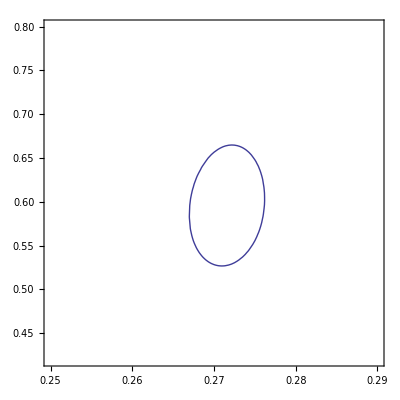
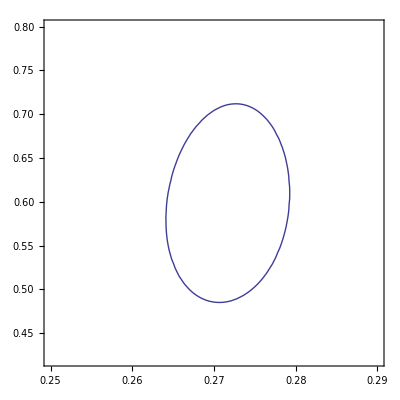
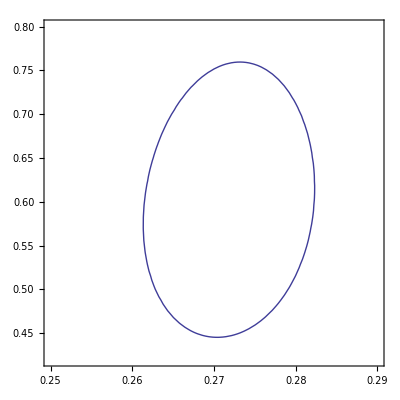

```mathematica
contoursall=ParallelTable[ContourPlot[chi21[om,g0]==fmin1[[2,1]]+dx2[[k]],{om,0.25,.29},{g0,.42,.8},AspectRatio->1,Frame->True,Axes->False],{k,1,3},DistributedContexts->Automatic]
```

```mathematica
Export[".\\backups\\contour_s8_0.8_Starob_G0_1s.m",contoursall[[1]]]
Export[".\\backups\\contour_s8_0.8_Starob_G0_2s.m",contoursall[[2]]]
Export[".\\backups\\contour_s8_0.8_Starob_G0_3s.m",contoursall[[3]]]
```

.\backups\contour_s8_0.8_Starob_G0_1s.m

.\backups\contour_s8_0.8_Starob_G0_2s.m

.\backups\contour_s8_0.8_Starob_G0_3s.m

```mathematica
cont1s=contoursall[[1]];
cont2s=contoursall[[2]];
cont3s=contoursall[[3]];
```

```mathematica
cont1s=Import[".\\backups\\contour_s8_0.8_Starob_G0_1s.m"];
cont2s=Import[".\\backups\\contour_s8_0.8_Starob_G0_2s.m"];
cont3s=Import[".\\backups\\contour_s8_0.8_Starob_G0_3s.m"];
```

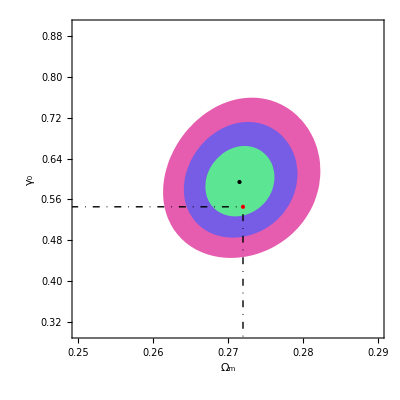

```mathematica
cont=Show[Graphics[Style[{Hue[0.9,.6,.9],Polygon[cont3s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.7,.6,.9],Polygon[cont2s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.4,.6,.9],Polygon[cont1s[[1,1]]]},Antialiasing->True],Frame->True],AspectRatio->1,PlotRange->{{0.25,.29},{.3,.9}},FrameLabel->{"Ω_m","γ_0"},Epilog->{{Black,PointSize[Large],Point[{om0,g00}]},{Red,PointSize[Large],Point[{0.272,6/11}]},{DotDashed,Line[{{0,6/11},{0.272,6/11}}],{DotDashed,Line[{{0.272,0},{0.272,6/11}}]}}},TextStyle->{FontFamily->"Times",FontSize->22},PlotRangeClipping->True]
```

```mathematica
output=".\\plots\\contours_Starob_s8_0.8_G0_om_g0";
Export[output<>".eps",cont,ImageSize->600];
Export[output<>".pdf",cont,ImageSize->600];
(*
Export[deaddrop<>"\\"<>output<>".eps",cont,ImageSize->600];
Export[deaddrop<>"\\"<>output<>".pdf",cont,ImageSize->600];
*)
```

```mathematica
(* end *)
```

```mathematica
(* Case 1 *)
```

```mathematica
om0=fmin2[[2,2,1,2]];
b0=fmin2[[2,2,2,2]];
g00=fmin2[[2,2,3,2]];
g10=fmin2[[2,2,4,2]];
chi20=chi2R[om0,0,b0,0]+chi2bao[om0,0,b0,0]+chi2SN[om0,0,b0,0];
chi21[g0_,g1_]:=chi20+chi2growth[om0,0,b0,0,g0,g1,σ80,1]
```

```mathematica
(* lim1=FindRoot[{chi21[w0,wa]==fmin1w0wa[[2,1]]+2.30,D[chi21[w0,wa],wa]==0},{{w0,-1.5},{wa,1.5}}] *)
```

```mathematica
fmin2
```

{3332.680657,{573.857,{om→0.272152,b→0.150043,g0→0.566529,g1→0.113377}}}

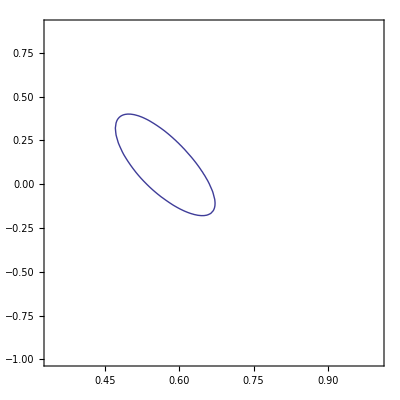
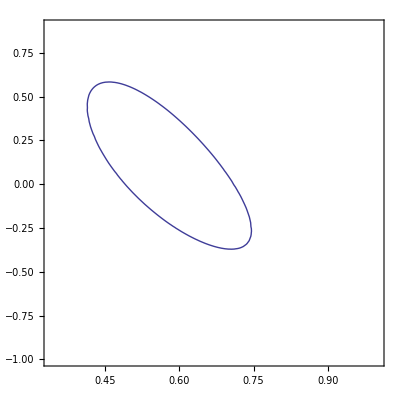
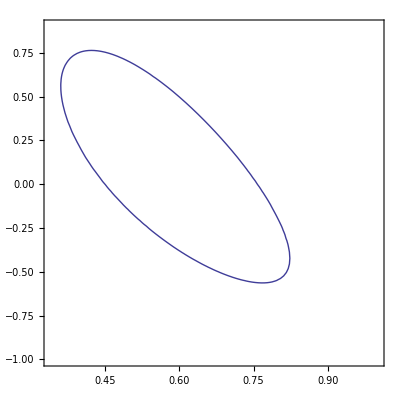

```mathematica
contoursall=ParallelTable[ContourPlot[chi21[g0,g1]==fmin2[[2,1]]+dx2[[k]],{g0,0.34,1},{g1,-1,.9},AspectRatio->1,Frame->True,Axes->False],{k,1,3},DistributedContexts->Automatic]
```

```mathematica
Export[".\\backups\\contour_s8_0.8_Starob_G1_1s.m",contoursall[[1]]]
Export[".\\backups\\contour_s8_0.8_Starob_G1_2s.m",contoursall[[2]]]
Export[".\\backups\\contour_s8_0.8_Starob_G1_3s.m",contoursall[[3]]]
```

.\backups\contour_s8_0.8_Starob_G1_1s.m

.\backups\contour_s8_0.8_Starob_G1_2s.m

.\backups\contour_s8_0.8_Starob_G1_3s.m

```mathematica
cont1s=contoursall[[1]];
cont2s=contoursall[[2]];
cont3s=contoursall[[3]];
```

```mathematica
cont1s=Import[".\\backups\\contour_s8_0.8_Starob_G1_1s.m"];
cont2s=Import[".\\backups\\contour_s8_0.8_Starob_G1_2s.m"];
cont3s=Import[".\\backups\\contour_s8_0.8_Starob_G1_3s.m"];
```

```mathematica
g1om=1/(yp0 Log[om])(om^g0+3wDE0(g0-1/2)(1-om)-3/2 Q0 om^(1-g0)+1/2)//FullSimplify;
yp0=1;
wDE0=weff=-1-1/3D[Log[H[Exp[Nn],om0,0,b0,0]^2-om0 Exp[-3 Nn]-Ωr Exp[-4 Nn]],Nn]/.Nn->0
Q0=Geffz[0,om0,b0]
```

-0.998295

1.01497

```mathematica
g1om01=g1om/.g0->6/11/.om->om0
g1om02=g1om/.g0->g00/.om->om0
```

-0.0384185

0.0251071

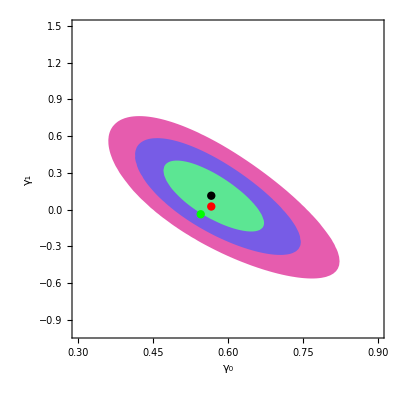

```mathematica
cont=ShowLegend[Show[Graphics[Style[{Hue[0.9,.6,.9],Polygon[cont3s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.7,.6,.9],Polygon[cont2s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.4,.6,.9],Polygon[cont1s[[1,1]]]},Antialiasing->True],Frame->True],AspectRatio->1,PlotRange->{{0.3,.9},{-1,1.5}},FrameLabel->{"γ_0","γ_1"},Epilog->{{Black,PointSize[.015],Point[{g00,g10}]},{Green,PointSize[.015],Point[{6/11,g1om01}]},{Red,PointSize[.015],Point[{g00,g1om02}]}},TextStyle->{FontFamily->"Times",FontSize->22},PlotRangeClipping->True],{{{Graphics[{PointSize[.3],Green,Point[{0,0}]}],Style["Σ_1",Large]},{Graphics[{PointSize[.3],Red,Point[{0,0}]}],Style["Σ_2",Large]},
{Graphics[{PointSize[.3],Black,Point[{0,0}]}],Style["BF",Large]}},LegendPosition->{.5,.35},LegendShadow->None,LegendSize->.4}]
```

```mathematica
output=".\\plots\\contours_Starob_s8_0.8_G1_g0_g1";
Export[output<>".eps",cont,ImageSize->600];
Export[output<>".pdf",cont,ImageSize->600];
(*
Export[deaddrop<>"\\"<>output<>".eps",cont,ImageSize->600];
Export[deaddrop<>"\\"<>output<>".pdf",cont,ImageSize->600];
*)
```

```mathematica
(* end *)
```

```mathematica
(* Case 2 *)
```

```mathematica
om0=fmin3[[2,2,1,2]];
b0=fmin3[[2,2,2,2]];
g00=fmin3[[2,2,3,2]];
g10=fmin3[[2,2,4,2]];
chi20=chi2R[om0,0,b0,0]+chi2bao[om0,0,b0,0]+chi2SN[om0,0,b0,0];
chi21[g0_,g1_]:=chi20+chi2growth[om0,0,b0,0,g0,g1,σ80,2]
```

```mathematica
(* lim1=FindRoot[{chi21[w0,wa]==fmin1w0wa[[2,1]]+2.30,D[chi21[w0,wa],wa]==0},{{w0,-1.5},{wa,1.5}}] *)
```

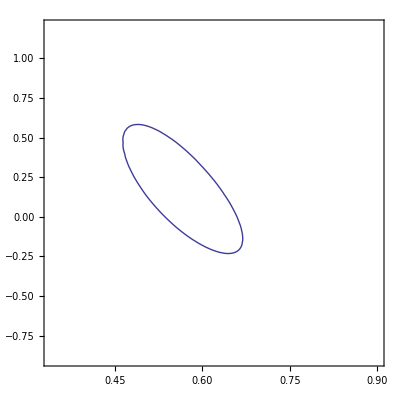
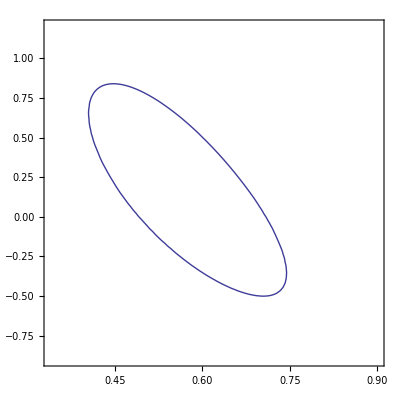
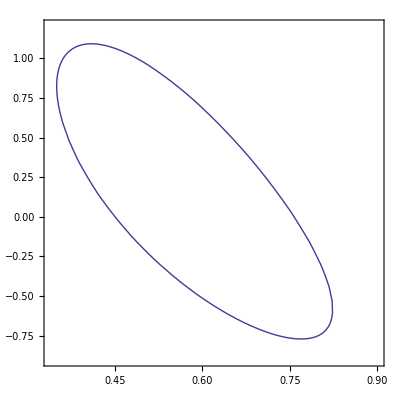

```mathematica
contoursall=ParallelTable[ContourPlot[chi21[g0,g1]==fmin3[[2,1]]+dx2[[k]],{g0,0.34,.9},{g1,-.9,1.2},AspectRatio->1,Frame->True,Axes->False],{k,1,3},DistributedContexts->Automatic]
```

```mathematica
Export[".\\backups\\contour_s8_0.8_Starob_G2_1s.m",contoursall[[1]]]
Export[".\\backups\\contour_s8_0.8_Starob_G2_2s.m",contoursall[[2]]]
Export[".\\backups\\contour_s8_0.8_Starob_G2_3s.m",contoursall[[3]]]
```

.\backups\contour_s8_0.8_Starob_G2_1s.m

.\backups\contour_s8_0.8_Starob_G2_2s.m

.\backups\contour_s8_0.8_Starob_G2_3s.m

```mathematica
cont1s=contoursall[[1]];
cont2s=contoursall[[2]];
cont3s=contoursall[[3]];
```

```mathematica
cont1s=Import[".\\backups\\contour_s8_0.8_Starob_G2_1s.m"];
cont2s=Import[".\\backups\\contour_s8_0.8_Starob_G2_2s.m"];
cont3s=Import[".\\backups\\contour_s8_0.8_Starob_G2_3s.m"];
```

```mathematica
g1om=1/(yp0 Log[om])(om^g0+3wDE0(g0-1/2)(1-om)-3/2 Q0 om^(1-g0)+1/2)//FullSimplify;
yp0=1;
wDE0=weff=-1-1/3D[Log[H[Exp[Nn],om0,0,b0,0]^2-om0 Exp[-3 Nn]-Ωr Exp[-4 Nn]],Nn]/.Nn->0
Q0=Geffz[0,om0,b0]
```

-0.998315

1.01489

```mathematica
g1om01=g1om/.g0->6/11/.om->om0
g1om02=g1om/.g0->g00/.om->om0
```

-0.0384178

0.0098037

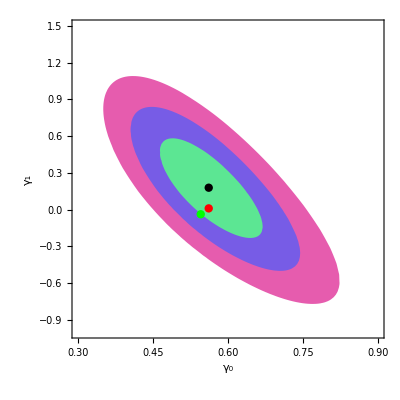

```mathematica
cont=ShowLegend[Show[Graphics[Style[{Hue[0.9,.6,.9],Polygon[cont3s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.7,.6,.9],Polygon[cont2s[[1,1]]]},Antialiasing->True],Frame->True],Graphics[Style[{Hue[0.4,.6,.9],Polygon[cont1s[[1,1]]]},Antialiasing->True],Frame->True],AspectRatio->1,PlotRange->{{0.3,.9},{-1,1.5}},FrameLabel->{"γ_0","γ_1"},Epilog->{{Black,PointSize[.015],Point[{g00,g10}]},{Green,PointSize[.015],Point[{6/11,g1om01}]},{Red,PointSize[.015],Point[{g00,g1om02}]}},TextStyle->{FontFamily->"Times",FontSize->22},PlotRangeClipping->True],{{{Graphics[{PointSize[.3],Green,Point[{0,0}]}],Style["Σ_1",Large]},{Graphics[{PointSize[.3],Red,Point[{0,0}]}],Style["Σ_2",Large]},
{Graphics[{PointSize[.3],Black,Point[{0,0}]}],Style["BF",Large]}},LegendPosition->{.5,.35},LegendShadow->None,LegendSize->.4}]
```

```mathematica
output=".\\plots\\contours_Starob_s8_0.8_G2_g0_g1";
Export[output<>".eps",cont,ImageSize->600];
Export[output<>".pdf",cont,ImageSize->600];
(*
Export[deaddrop<>"\\"<>output<>".eps",cont,ImageSize->600];
Export[deaddrop<>"\\"<>output<>".pdf",cont,ImageSize->600];
*)
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* fσ8(z) *)
```

```mathematica
{fσ8z[1,om,0,b,0,g0,0,σ80,0]/.fmin1[[2,2]],fσ8z[1,om,0,b,0,g0,g1,σ80,1]/.fmin2[[2,2]],fσ8z[1,om,0,b,0,g0,g1,σ80,2]/.fmin3[[2,2]],fσ8wCDM[1,-1,0.273,0.8]}
```

{0.424091,0.421869,0.418996,0.424919}

```mathematica
plgr=ErrorListPlot[datagrowth,PlotRange->All,PlotStyle->Gray];
```

```mathematica
pl1=Plot[{fσ8z[z,om,0,b,0,g0,0,σ80,0]/.fmin1[[2,2]],fσ8z[z,om,0,b,0,g0,g1,σ80,1]/.fmin2[[2,2]],fσ8z[z,om,0,b,0,g0,g1,σ80,2]/.fmin3[[2,2]],fσ8wCDM[z,-1,0.273,0.8]},{z,0,0.8},PlotRange->All,PlotStyle->{Blue,Green,Red,Black}];
```

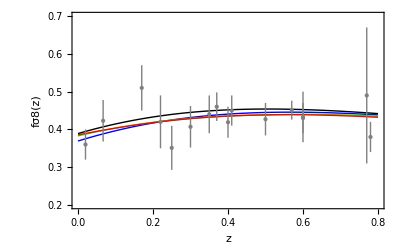

```mathematica
fs8pl=ShowLegend[Show[pl1,plgr,PlotRange->{All,{0.2,.7}},Axes->False,Frame->True,FrameLabel->{"z","fσ8(z)"}],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"f_2+Γ_0"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"f_2+Γ_1"},
{Graphics[{Red,Line[{{0,0},{1,0}}]}],"f_2+Γ_2"},
{Graphics[{Black,Line[{{0,0},{1,0}}]}],"ΛCDM"}},LegendPosition->{.9,-.3},LegendShadow->None}]
```

```mathematica
Export[".\\plots\\fs8(z)_s8_0.8_Starob.eps",fs8pl,ImageSize->500]
Export[".\\plots\\fs8(z)_s8_0.8_Starob.pdf",fs8pl,ImageSize->500]
```

.\backups\fs8(z)_s8_0.8_Starob.eps

.\backups\fs8(z)_s8_0.8_Starob.pdf

```mathematica
(* end *)
```

```mathematica
(* γ(z) *)
```

```mathematica
{γ[0][.1,g0,0]/.fmin1[[2,2]],γ[1][.1,g0,g1]/.fmin2[[2,2]],γ[2][.1,g0,g1]/.fmin3[[2,2]],6/11.}
```

{0.594131,0.577867,0.577713,0.545455}

```mathematica
cij1sm=cij1[[3,3]];
cij2sm=cij2[[3;;4,3;;4]];
cij3sm=cij3[[3;;4,3;;4]];
```

```mathematica
sg1[z_]:=(Sum[D[γ[1][z,g0,g1],{g0,g1}[[i]]]D[γ[1][z,g0,g1],{g0,g1}[[j]]] cij2sm[[i,j]],{i,1,2},{j,1,2}])^(1/2)
sg2[z_]:=(Sum[D[γ[2][z,g0,g1],{g0,g1}[[i]]]D[γ[2][z,g0,g1],{g0,g1}[[j]]] cij3sm[[i,j]],{i,1,2},{j,1,2}])^(1/2)
```

```mathematica
pl0=Plot[{γ[0][z,g0,0]+√cij1sm-6/11./.fmin1[[2,2]],γ[0][z,g0,0]-6/11./.fmin1[[2,2]],γ[0][z,g0,0]-√cij1sm-6/11./.fmin1[[2,2]]},{z,0,1},PlotRange->All,PlotStyle->{{Dashed,Blue},Blue,{Dashed,Blue}},BaseStyle->{FontFamily->"Times",FontSize->20}];
pl1=Plot[{(γ[1][z,g0,g1]+sg1[z]-6/11.)/.fmin2[[2,2]],(γ[1][z,g0,g1]-6/11.)/.fmin2[[2,2]],(γ[1][z,g0,g1]-sg1[z]-6/11.)/.fmin2[[2,2]]},{z,0,1},PlotRange->All,PlotStyle->{{Dashed,Green},Green,{Dashed,Green}},BaseStyle->{FontFamily->"Times",FontSize->20}];
pl2=Plot[{γ[2][z,g0,g1]+sg2[z]-6/11./.fmin3[[2,2]],γ[2][z,g0,g1]-6/11./.fmin3[[2,2]],γ[2][z,g0,g1]-sg2[z]-6/11./.fmin3[[2,2]]},{z,0,1},PlotRange->All,PlotStyle->{{Dashed,Red},Red,{Dashed,Red}},BaseStyle->{FontFamily->"Times",FontSize->20}];
```

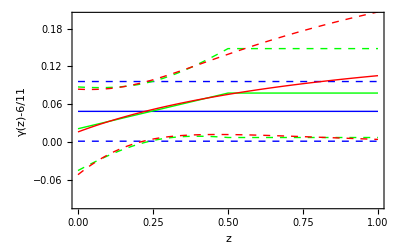

```mathematica
plg1=ShowLegend[Show[pl0,pl1,pl2,PlotRange->{All,{-.1,0.2}},Axes->False,Frame->True,FrameLabel->{"z","γ(z)-6/11"}],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],Style["Γ_0",Large]},{Graphics[{Green,Line[{{0,0},{1,0}}]}],Style["Γ_1",Large]},
{Graphics[{Red,Line[{{0,0},{1,0}}]}],Style["Γ_2",Large]}},LegendPosition->{.9,-.1},LegendSize->.4,LegendShadow->None}]
```

```mathematica
Export[".\\plots\\gamma(z)_s8_0.8_Starob.eps",plg1,ImageSize->500]
Export[".\\plots\\gamma(z)_s8_0.8_Starob.pdf",plg1,ImageSize->500]
```

.\plots\gamma(z)_s8_0.8_Starob.eps

.\plots\gamma(z)_s8_0.8_Starob.pdf

```mathematica
(* end *)
```

```mathematica
(* Geff(z) *)
```

```mathematica
fmin1[[2,2]]
fmin2[[2,2]]
fmin3[[2,2]]
```

{om→0.271532,b→0.291657,g0→0.594131}

{om→0.272152,b→0.150043,g0→0.566529,g1→0.113377}

{om→0.272158,b→0.14916,g0→0.561458,g1→0.178806}

```mathematica
LaunchKernels[3];
```

```mathematica
om01=fmin1[[2,2,1,2]];
b01=fmin1[[2,2,2,2]];
om02=fmin2[[2,2,1,2]];
b02=fmin2[[2,2,2,2]];
om03=fmin3[[2,2,1,2]];
b03=fmin3[[2,2,2,2]];
```

```mathematica
dG[z_,om_,b_,{p_,p0_}]:=(dG[z,om,b,{p,p0}]=ND[Geffz[z,om,b],p,p0]//Chop)
sG[z_,om0_,b0_,cij_]:=(Sum[{dG[z,om,b0,{om,om0}],dG[z,om0,b,{b,b0}]}[[i]] {dG[z,om,b0,{om,om0}],dG[z,om0,b,{b,b0}]}[[j]]cij[[i,j]],{i,1,2},{j,1,2}])^(1/2)//Re;
```

```mathematica
errorGeff1=Interpolation[ParallelTable[{z,sG[z,om01,b01,cij1]},{z,0,2,0.5},DistributedContexts->Automatic]];
errorGeff2=Interpolation[ParallelTable[{z,sG[z,om02,b02,cij2]},{z,0,2,0.5},DistributedContexts->Automatic]];
errorGeff3=Interpolation[ParallelTable[{z,sG[z,om03,b03,cij3]},{z,0,2,0.5},DistributedContexts->Automatic]];
```

```mathematica
pl1=Plot[{Geffz[zz,om01,b01]+errorGeff1[zz],Geffz[zz,om01,b01],Geffz[zz,om01,b01]-errorGeff1[zz]},{zz,0,1.5},PlotStyle->{Gray,Black,Gray},Filling->{1->{{3},Gray}},PlotRange->{{0.,1.5},{0.98,1.04}}];
```

```mathematica
pl2=Plot[{Geffz[zz,om02,b02]+errorGeff1[zz],Geffz[zz,om02,b02],Geffz[zz,om02,b02]-errorGeff1[zz]},{zz,0,1.5},PlotStyle->{Gray,Black,Gray},Filling->{1->{{3},Gray}},PlotRange->{{0.,1.5},{0.98,1.04}}];
```

```mathematica
pl3=Plot[{Geffz[zz,om03,b03]+errorGeff1[zz],Geffz[zz,om03,b03],Geffz[zz,om03,b03]-errorGeff1[zz]},{zz,0,1.5},PlotStyle->{Gray,Black,Gray},Filling->{1->{{3},Gray}},PlotRange->{{0.,1.5},{0.98,1.04}}];
```

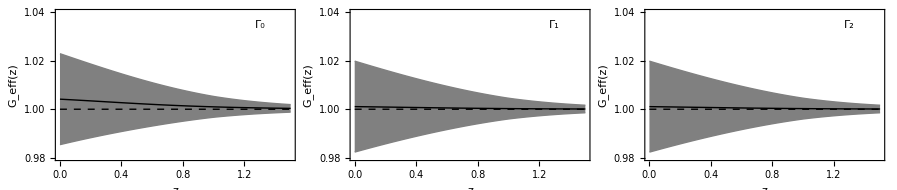

```mathematica
plgeff=GraphicsGrid[{{Show[pl1,Frame->True,FrameLabel->{"z","G_eff(z)"},Axes->False,PlotRange->{{0.,1.5},{0.98,1.04}},Epilog->{Text[Style["Γ_0",Large],{1.3,1.035}],{Dashed,Line[{{0,1},{2,1}}]}},BaseStyle->{FontSize->18,FontFamily->"Times"}],Show[pl2,Frame->True,FrameLabel->{"z","G_eff(z)"},Axes->False,PlotRange->{{0.,1.5},{0.98,1.04}},Epilog->{Text[Style["Γ_1",Large],{1.3,1.035}],{Dashed,Line[{{0,1},{2,1}}]}},BaseStyle->{FontSize->18,FontFamily->"Times"}],Show[pl3,Frame->True,FrameLabel->{"z","G_eff(z)"},Axes->False,PlotRange->{{0.,1.5},{0.98,1.04}},Epilog->{Text[Style["Γ_2",Large],{1.3,1.035}],{Dashed,Line[{{0,1},{2,1}}]}},BaseStyle->{FontSize->18,FontFamily->"Times"}]}},Spacings->-15]
```

```mathematica
Export[".\\plots\\Geff(z)_Starob_s8_0.8.eps",plgeff,ImageSize->1000]
Export[".\\plots\\Geff(z)_Starob_s8_0.8.pdf",plgeff,ImageSize->1000]
```

.\plots\Geff(z)_Starob_s8_0.8.eps

.\plots\Geff(z)_Starob_s8_0.8.pdf

```mathematica
(* end *)
```